Final Project Econ Modeling
Ellis Brown, Raviteja Kasturi, Austin Wortley
Modeling Venture Capital Decisions

In theory, utility should be measured relative to one’s total wealth for all possible scenarios over all time. In practice, if the range of gains and losses is small compared to our current wealth, we can ignore our wealth and limit the scenarios to those involving the investment only. Suppose our utility function is u. Suppose also that we have wealth w and that we face a lottery whose outcome is given by a probability distribution o and whose expected value EV[o] is zero. Since the lottery is as likely to decrease our wealth as to increase it, we would pay a small amount p, called the risk premium, to avoid playing this lottery. So the probability of a certain event is EV[u(w + o)] = u(w + EV[o] - p) = u(w - p). Expanding using Taylor series : EV[u(w) + o u’(w) + (o^2) u”(w)/2] = u(w) - p u’(w). So after simplifying : p = - (vˇ2) u”(w)/u’(w). Trying to solve for coefficients a and b

```mathematica
expU[w_]:=a1-b1 Exp[-w/rho];
logU[w_]:=a2+b2 Log[w+rho];
```

The parameter rho is sometimes called the “risk-tolerance” or “risk-aversion coefficient” because of its relation to the absolute risk aversion. For the exponential utility function:

```mathematica
-expU''[w]/expU'[w]
```

1/rho

```mathematica
-logU''[w]/logU'[w]
```

1/(rho+w)

Set the low  and high (0, 1.5) to be equal 0 or 100 in utility, same for log U

```mathematica
eqns={expU[0]==0,expU[1.5]==100,logU[0]==0,logU[1.5]==100}
```

{a1-b1==0,a1-b1 ⅇ^(-1.5/rho)==100,a2+b2 Log[rho]==0,a2+b2 Log[1.5+rho]==100}

```mathematica
Solve[eqns/.rho->0.3,{a1,a2,b1,b2}]//First
```

{a1→100.678,a2→67.195,b1→100.678,b2→55.8111}

```mathematica
{expU[w_],logU[w_]}={expU[w],logU[w]}/.%/.rho->0.3
```

{100.678-100.678 ⅇ^(-3.33333 w),67.195+55.8111 Log[0.3+w]}

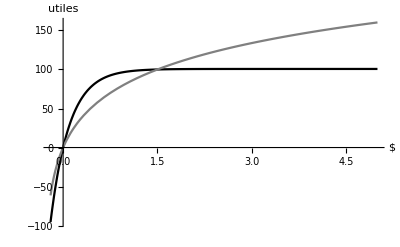

```mathematica
Plot[{expU[w],logU[w]},{w,-0.2,5},AxesLabel->{"$","utiles"},PlotRange->All,PlotStyle->{GrayLevel[0],GrayLevel[0.5]}]
```

We have chosen the parameters of the two utility functions so that their behavior is similar near zero. The exponential function appears almost flat for large w, so outcomes are regarded as nearly the same. The logarithmic utility function increases more rapidly, so larger risks are tolerated as wealth increases.

Let’s look at a simple example of how the utility functions are used in decision making. Suppose I offer you a choice oftwo lotteries. The first lottery is a 0.75 chance at a pound of American cheese ($2 10-6 million) and a 0.25 chance at a Mercedes Benz ($60 10-3 million). The second is a 50-50 chance at a Geo Metro ($7 10-3 million) and a Mazda Miata ($20 10-3 million). Which of these two lotteries do you prefer?

Your preference will be determined by the choice of a utility function. Let’s apply both the exponential and logarithmic utility functions. The first lottery has exponential utilities of:

```mathematica
Map[expU,{2 10^-6,60 10^-3}]
```

{0.000671187,18.2499}

The expected utility is the inner product of the probabilities and these utilities:

```mathematica
{0.75,0.25}.%
```

4.56298

The second lottery has a lower expected utility:

```mathematica
Map[expU,{7 10^-3,20 10^-3}]
```

{2.32197,6.49305}

```mathematica
{0.5,0.5}.%
```

4.40751

Since the first lottery has the higher expected utility, you would always choose it. Now let’s apply the logarithmic utility function. For the first lottery, the utilities are:

```mathematica
Map[logU,{2 10^-6,60 10^-3}]
```

{0.000372073,10.1756}

Expected Utility:

```mathematica
eu={0.75,0.25}.%
```

2.54417

For the second lottery:

```mathematica
Map[logU,{7 10^-3,20 10^-3}]
```

{1.2873,3.60196}

```mathematica
{0.5,0.5}.%
```

2.44463

Again, the first lottery has the higher expected utility, so you would always choose it. Suppose we already owned the right to play the first lottery for the Mercedes. What price would we sell it for? The certain equivalent is the amount whose utility is equal to the expected utility of the lottery. Using the logarithmic utility, we get:

```mathematica
FindRoot[eu==logU[ce],{ce,0}]
```

{ce→0.0139921}

Thus, we would sell the right to play the first lottery for $13,992.10.